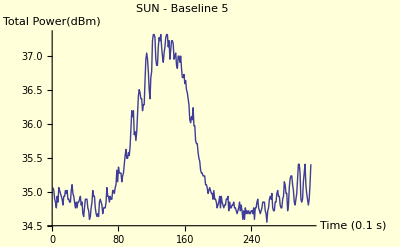

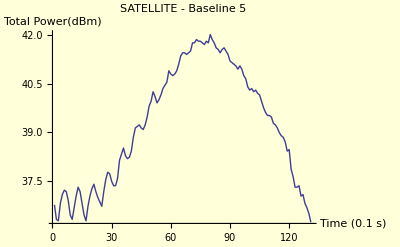

```mathematica
(* MAIN CODE TO FIND THE DIAMETER OF THE SUN BY INTERFEROMETRY *)

m=5;

(* CONSTANTS *) 
ω = 360 Degree /(24*3600);
f = 1000*10^7;
λ = 2.99792485*^10/f;
intTime = 100;
vpslope = -25;
suncut = 50;
satcut = suncut/2;
offsetsun = 20;
offsetsat = offsetsun/2;
azimsun = {155.2,162.3, 162, 165.4, 165.4 };
δsun =     ArcSin [Sin[-23.44 Degree]*Sin[ azimsun[[m]] Degree]] ;
δsat =     ArcSin [Sin[-23.44 Degree]*Sin[154.1 Degree]] ;
intTime = 100;
timepersweep = 25;


(* OPENING FILES AND CREATING TABLES *)
SAT = Import["/home/marina/Desktop/ana/SAT/SAT"<>ToString[m]<>".dat","Table"];
SUN = Import["/home/marina/Desktop/ana/SUN/SUN"<>ToString[m]<>".dat","Table"];

(* FIXING POSITIVE VALUES AND FRACTIONAL TIME *)
A=Table[{SUN[[i]][[1]],Exp[2-SUN[[i]][[2]]]},{i,1,Length[SUN]}];
B=Table[{SAT[[i]][[1]],Exp[2-SAT[[i]][[2]]]},{i,1,Length[SAT]}];
A1=Table[0,{1}];
B1=Table[0,{1}];

suncurve=Transpose[A]; 
satcurve=Transpose[B]; 

(* CONVERTING FROM VOLT TO TOTAL POWER *)
timesun = suncurve[[1]];
psun= suncurve[[2]]*(-vpslope);
timesat = satcurve[[1]];
psat= satcurve[[2]]*(-vpslope);

ListLinePlot[psun,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],PlotRange->All,AxesLabel->{"Time (0.1 s)","Total Power(dBm)"},PlotLabel->"SUN  - Baseline  "<>ToString[m] ,LabelStyle->Directive[Bold,Medium]] 
ListLinePlot[psat,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],PlotRange->All,AxesLabel->{"Time (0.1 s)","Total Power(dBm)"},PlotLabel->"SATELLITE  - Baseline  "<>ToString[m] ,LabelStyle->Directive[Bold,Medium]]
```

```mathematica
(* CONVERTING TOTAL POWER IN dBm TO mW *)
suncurve= 10^((psun+30)/(10));
satcurve= 10^((psat+30)/(10));
Tsatpow= Table[{j,satcurve[[j]]},{j, Length[satcurve]}];
Tsunpow= Table[{j,suncurve[[j]]},{j, Length[suncurve]}];
```

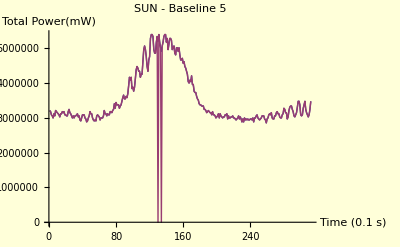

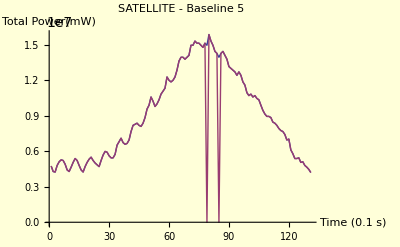

```mathematica
(* CALCULATING PMAX AND PMIN *)
MAsun = suncurve;
PPmaxsun = Floor[Median[Flatten[Position[MAsun,Max[MAsun]]]]];
Pmaxsun = MAsun[[PPmaxsun]];
For[i=PPmaxsun, i>20, --i,
If[MAsun [[i-1]]>MAsun[[i]],
PPminLeftsun= i; Break[],
False
];
];
For[i=PPmaxsun, i<Length[MAsun], ++i,
If[MAsun[[i+1]]>MAsun[[i]],
PPminRightsun = i; Break[],
False
];
];
Pminsun= Mean[{MAsun[[PPminLeftsun+suncut]],MAsun[[PPminRightsun+suncut]]}];

MAsat = satcurve;
PPmaxsat= Floor[Median[Flatten[Position[MAsat,Max[MAsat]]]]];
Pmaxsat= MAsat[[PPmaxsat]];
For[i=PPmaxsat, i>20, --i,
If[MAsat [[i-1]]>MAsat[[i]],
PPminLeftsat= i; Break[],
False
];
];

For[i=PPmaxsat, i<Length[MAsat], ++i,
If[MAsat[[i+1]]>MAsat[[i]],
PPminRightsat = i; Break[],
False
];
];
Pminsat= Mean[{MAsat[[PPminLeftsat+satcut]],MAsat[[PPminRightsat+satcut]]}];

cMChecksun=MAsun;
cMChecksun[[PPminLeftsun]] =0;
cMChecksun[[PPminRightsun]]=0;
ListLinePlot[{MAsun,cMChecksun}, Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue], PlotRange->All,AxesLabel->{"Time (0.1 s)","Total Power(mW)"},PlotLabel->"SUN  - Baseline  "<>ToString[m] ,LabelStyle->Directive[Bold,Medium]]
cMChecksat = MAsat;
cMChecksat[[PPminLeftsat]] =0;
cMChecksat[[PPminRightsat]]=0;
ListLinePlot[{MAsat,cMChecksat}, Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],PlotRange->All,AxesLabel->{"Time (0.1 s)","Total Power(mW)"},PlotLabel->"SATELLITE  - Baseline  "<>ToString[m],LabelStyle->Directive[Bold,Medium]]
```

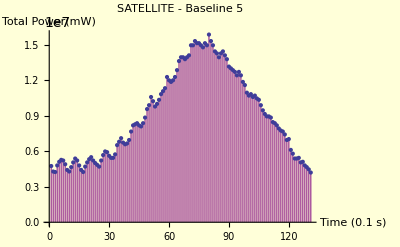

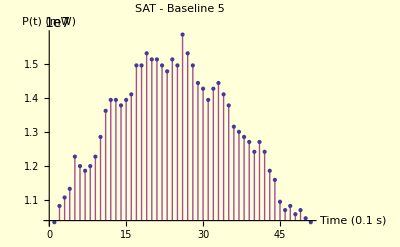

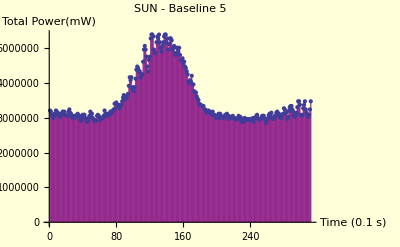

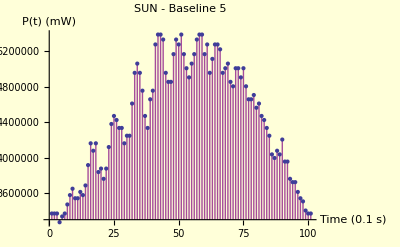

```mathematica
(* CUTTING UNNECESSARY POINTS AND PLOTING *)
Tsat=Table[Tsatpow[[k]][[2]],{k,PPmaxsat-satcut,PPmaxsat+satcut}];
Tsun = Table[ Tsunpow[[k]][[2]], { k, PPmaxsun-suncut, PPmaxsun+ suncut}] ;
ListPlot[satcurve,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],Purple],Filling->Axis,AxesLabel->{"Time (0.1 s)","Total Power(mW)"},PlotLabel->"SATELLITE - Baseline  "<>ToString[m],LabelStyle->Directive[Bold,Medium]]
ListPlot[Tsat,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],Purple],Filling->Axis,AxesLabel->{"Time (0.1 s)"," P(t) (mW)"},PlotLabel->"SAT - Baseline "<>ToString[m],LabelStyle->Directive[Bold,Medium]]
ListPlot[suncurve,   Background->LightYellow, FillingStyle->Directive[Opacity[0.7],Purple],Filling->Axis,
AxesLabel->{"Time (0.1 s)","Total Power(mW)"},PlotLabel->"SUN - Baseline  "<>ToString[m],LabelStyle->Directive[Bold,Medium]]
ListPlot[Tsun,   Background->LightYellow, FillingStyle->Directive[Opacity[0.7],Purple],Filling->Axis,
AxesLabel-> {"Time (0.1 s)"," P(t) (mW)"}, PlotLabel->"SUN - Baseline "<>ToString[m],LabelStyle->Directive[Bold,Medium]]


(* FOURIER TRANSFORMING *)
cFFTsun=Abs[Fourier[MAsun]];
cFFTsat=Abs[Fourier[MAsat]];
ListLinePlot[cFFTsun,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],AxesLabel->{"Freq","Fourier Comp"},PlotLabel->"SUN  - Baseline  "<>ToString[m],LabelStyle->Directive[Bold,Medium]];
ListPlot[cFFTsun,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],Filling->Axis,AxesLabel->{"Freq","FFT"},PlotLabel->"SAT - Baseline "<>ToString[m],LabelStyle->Directive[Bold,Medium]];
ListLinePlot[cFFTsat, Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],AxesLabel->{"Freq","Fourier Comp"},PlotLabel->"SATELLITE  - Baseline  "<>ToString[m],LabelStyle->Directive[Bold,Medium]];
ListPlot[cFFTsat,Background->LightYellow,FillingStyle->Directive[Opacity[0.7],LightBlue],Filling->Axis,AxesLabel->{"Freq)","FFT"},PlotLabel->"SAT - Baseline "<>ToString[m],LabelStyle->Directive[Bold,Medium]];
```

```mathematica
(* CALCUATING THE BASELINE VALUES in cm*)
fringeFreqsun = Flatten[Position[Take[cFFTsun,{offsetsun,Length[cFFTsun]}],Max[Take[cFFTsun,{offsetsun,Length[cFFTsun]/2//Floor}]]]][[1]] +offsetsun -1;
fringeTimesun = 1/(fringeFreqsun/(Length[cFFTsun]*timepersweep));
fringeFreqsat = Flatten[Position[Take[cFFTsat,{offsetsat,Length[cFFTsat]}],Max[Take[cFFTsat,{offsetsat,Length[cFFTsat]/2//Floor}]]]][[1]] +offsetsat-1;
fringeTimesat= 1/(fringeFreqsat/(Length[cFFTsat]*timepersweep));
dCalcsun = λ/(Cos[ δsun]Sin[ω * fringeTimesun])
dCalcsat = λ/(Cos[ δsat]Sin[ω * fringeTimesat])
```

212.485

230.083

```mathematica
(* CALCULATING THE VISIBILITY FUNCTION VALUES *)
PPminsat = Floor[Median[Flatten[Position[MAsat,Min[MAsat]]]]];
Pminsat = MAsun[[PPminsat]];
v  = (Pmaxsun-Pminsun)/(Pmaxsun+Pminsun)
vsat  = (Pmaxsat-Pminsat)/(Pmaxsat+Pminsat)
```

0.23276

0.493103

```mathematica
(* CALCULATING THE ANGULAR DIAMETER OF THE SUN BY TAYLOR EXPANDING, UTILIZING THE BASELINES BY THE SUN AND BY THE SAT DATA *)
ϕ1=(Sqrt[6]/Pi)*(λ/dCalcsun)*Sqrt[1 -Abs[v]];
ϕ1min= ϕ1*(180/Pi)*60

ϕ2=(Sqrt[6]/Pi)*(λ/dCalcsat)*Sqrt[1 - Abs[v]];
ϕ2min= ϕ2*(180/Pi)*60
```

33.1251

30.5915